```mathematica
SymbolDepth[s_]:=Length[SymbolToSets[s]]
```

```mathematica
FormulaDepth[f_]:=Block[{depths=Map[SymbolDepth,ListofVars[f]]},
Max[depths]-Min[depths]+1]
```

```mathematica
FormulaBreath[f_]:=Block[{depths=Map[SymbolDepth,ListofVars[f]]},
Last[First[Sort[Tally[depths],#1[[2]]>#2[[2]]&]]]
]
```

```mathematica
depths=Table[k->{FormulaDepth[allGraphs5[k,"colofour"]],FormulaBreath[allGraphs5[k,"colofour"]],EdgeCount[FormulaGraphReverse[allGraphs5[k,"colofour"]]]},{k,Keys[allGraphs5]}];
```

```mathematica
TableForm[Sort[Tally[Map[Last,depths]],Last[#1]<Last[#2]&],TableDepth->1]
```

{{5,25,160},1}
{{2,4,4},5}
{{3,6,18},10}
{{3,9,28},10}
{{4,4,17},10}
{{4,19,92},10}
{{4,14,56},15}
{{4,7,30},15}
{{4,7,31},15}
{{4,10,42},20}
{{4,10,37},30}
{{3,3,7},30}
{{3,5,12},30}
{{4,14,60},30}
{{3,2,4},45}
{{1,1,0},52}
{{4,7,25},60}
{{4,10,38},60}
{{4,5,20},60}
{{4,7,26},60}
{{3,5,13},60}
{{3,4,10},60}
{{3,5,14},60}
{{3,6,20},60}
{{2,3,3},60}
{{3,3,6},75}
{{3,5,15},102}
{{3,4,8},105}
{{2,1,1},160}
{{3,3,5},180}
{{3,4,9},180}
{{2,2,2},225}

```mathematica
With[{k=lambdaKey},{FormulaDepth[allGraphs5[k,"colofour"]],FormulaBreath[allGraphs5[k,"colofour"]]}]
```

{2,5}

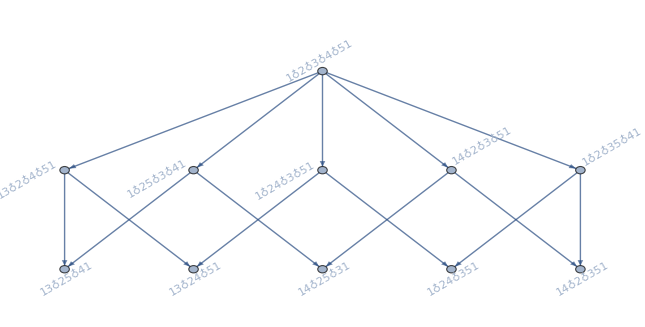

```mathematica
FormulaGraphReverse3[allGraphs5[lambdaKey,"colofour"]]
```

```mathematica
RandomSample[Select[depths,#[[2]]=={3,4}&],10]
```

{28782→{3,4},20772→{3,4},8788→{3,4},9030→{3,4},9082→{3,4},29484→{3,4},774→{3,4},9108→{3,4},9756→{3,4},9594→{3,4}}

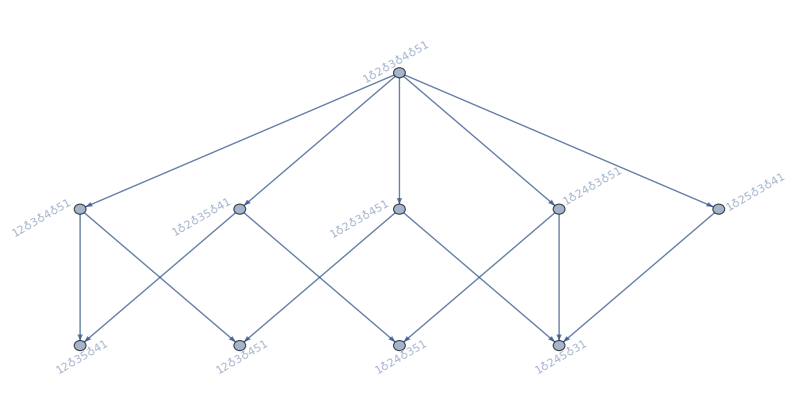
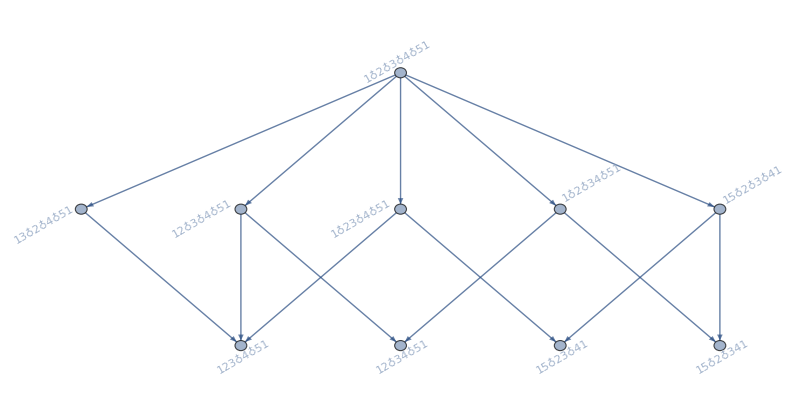
{-Graphics-97294→-Graphics-,-Graphics-22994→-Graphics-}

```mathematica
Table[ShowGraph5Least[k]->Graph[FormulaGraphReverse3[allGraphs5[k,"colofour"]],ImageSize->800],{k,Map[First,RandomSample[Select[depths,#[[2]]=={3,5,14}&],2]]}]
```

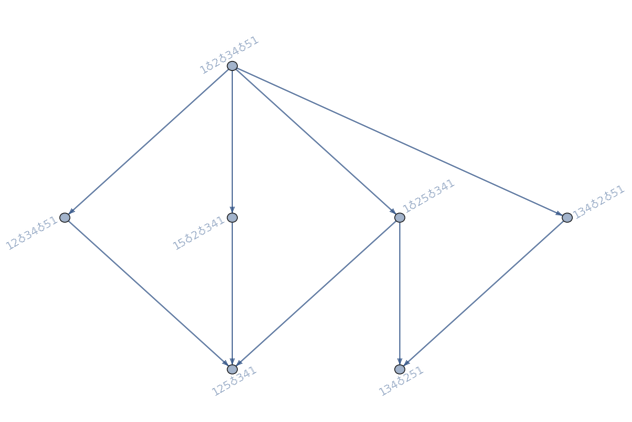

```mathematica
FormulaGraphReverse3[allGraphs5[346,"colofour"]]
```

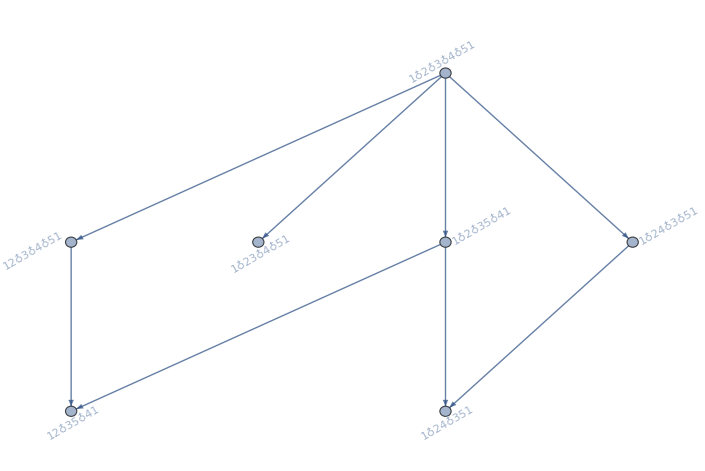

```mathematica
FormulaGraphReverse3[allGraphs5[9514,"colofour"]]
```

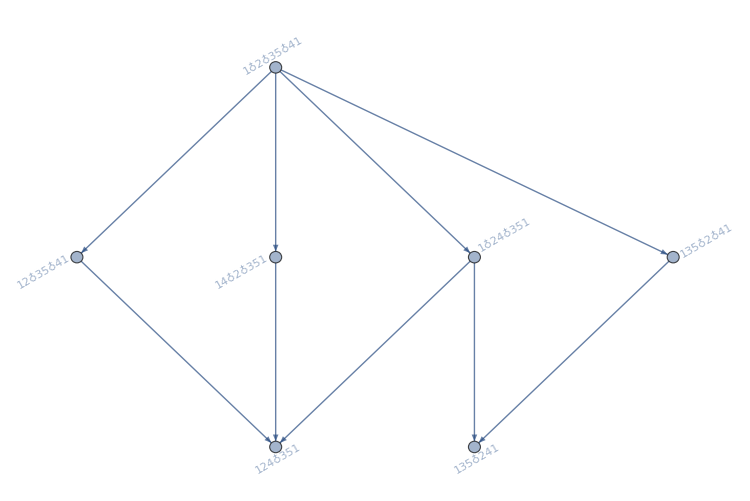

```mathematica
FormulaGraphReverse3[allGraphs5[286,"colofour"]]
```

```mathematica
allGraphs5[0,"colofour"]//FormulaBreath
```

25